```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ServiceLine`"];
```

```mathematica
arrival = Import["Data/Arrival.dat"];
```

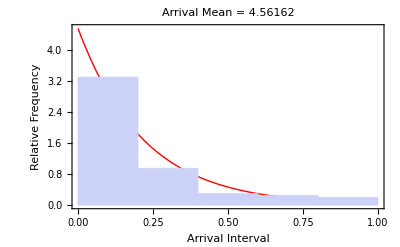

```mathematica
arrivalTime = Table[arrival[[i,2]],{i,2,Length[arrival]}];
PrettyPlot[arrivalTime]
```